## HNL

### Model description

```mathematica
LLPsel="HNL";
ModelDescription[LLPsel]=Row[{"Heavy Neutral Lepton N - a fermion with the phenomenological Lagrangian L = Y_α (L̄)_αiσ_2H^*N, where Y_α is the Yukawa coupling, H is the Higgs doublet, and L_α is the left lepton SU(2)_L doublet. Below the electroweak scale, HNLs have effective mixing with neutrinos ν_α given by the mixing angle U_α. Further, everything is expressed in terms of the squared mixing angles U_α^2 = U^2(x_e, x_μ, x_τ), where x_e+x_μ+x_τ = 1. See 1805.08567 for the phenomenology description. The models with x_e = 1 (and others zero), x_μ = 1 (and others zero), x_τ = 1 (and others zero) are known as BC6, BC7, BC8 within PBC benchmarking (1901.09966)"}];
filepheno=FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology","ModelDescriptors.mx"}];
rowtoadd={LLPsel,ModelDescription[LLPsel]};
If[!FileExistsQ[filepheno],
file={rowtoadd};
,
file=Import[filepheno,"MX"];
file=Join[Select[file,#[[1]]!=LLPsel&],{rowtoadd}];
]
Export[filepheno,SortBy[file,#[[1]]&],"MX"];
file;
```

### Importing lifetime

```mathematica
HNLsList={"HNL-mixing-e","HNL-mixing-mu","HNL-mixing-tau"};
Do[
DecayDescriptionExplanation[LLP,"Default"]="Description from 1805.08567, but with improved matching between hadronic decays described using pQCD and exclusively (dedicated merging for each mixing and charged/neutral current)";
,{LLP,HNLsList}]
Γtable=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology","HNL","decay widths","HNLdecayWidth.dat"}],"Table"];
{DecayWidth[mLLP_,U2_,HNLsList[[1]]],DecayWidth[mLLP_,U2_,HNLsList[[2]]],DecayWidth[mLLP_,U2_,HNLsList[[3]]]}=U2(10^Interpolation[{#[[1]],Log10[#[[2]]+10^-99]}&/@Γtable[[All,{1,#}]],InterpolationOrder->1][mLLP])&/@{2,3,4};
Do[
cτLLP[HNL,"Default",mLLP_,U2_]=chbar/DecayWidth[mLLP,U2,HNL];
couplingSymbol[HNL]=U2;
,{HNL,HNLsList}]
```

### List of decay processes and sets of decay products for them, branching ratios, and matrix elements

```mathematica
HNLdecaypheno0[mLLP_,E1_,E3_]=Import[FileNameJoin[{NotebookDirectory[]//ParentDirectory//ParentDirectory,"phenomenology/HNL/decay widths/HNLdecaysSensCalc.mx"}],"MX"];
(*Merging processes and charge conjugated ones, as for the practic purposes there is no difference*)
proclist=HNLdecaypheno0[mLLP,E1,E3][[All,1]];
HNLdecaypheno[mLLP_,E1_,E3_]={};
Do[
Module[{procbar},
If[!StringContainsQ[proc,"bar"],
procbar=proc<>"bar";
stringproc[mLLP_,E1_,E3_]=Select[HNLdecaypheno0[mLLP,E1,E3],#[[1]]==proc||#[[1]]==procbar&];
HNLdecaypheno[mLLP_,E1_,E3_]=Join[HNLdecaypheno[mLLP,E1,E3],{{stringproc[mLLP,E1,E3][[1]][[1]],stringproc[mLLP,E1,E3][[1]][[2]],Total[stringproc[mLLP,E1,E3][[All,3]]],Total[stringproc[mLLP,E1,E3][[All,4]]],Total[stringproc[mLLP,E1,E3][[All,5]]],stringproc[mLLP,E1,E3][[1]][[6]],stringproc[mLLP,E1,E3][[1]][[7]],stringproc[mLLP,E1,E3][[1]][[8]]}}]
]
]
,{proc,proclist}]
(*e mixing*)
LLPsel=HNLsList[[1]];
{channelsnonzero[HNLsList[[1]],mLLP_,E1_,E3_],channelsnonzero[HNLsList[[2]],mLLP_,E1_,E3_],channelsnonzero[HNLsList[[3]],mLLP_,E1_,E3_]}=Table[Select[HNLdecaypheno[mLLP,E1,E3],!FreeQ[#[[i]],0]&][[All,{1,2,i,3+i}]],{i,{3,4,5}}];
Do[
ProcessesList[hnl,"True"]=channelsnonzero[hnl,mLLP,E1,E3][[All,1]];
Do[
Module[{proc},
proc=ProcessesList[hnl,"True"][[i]];
ListDecayProducts[hnl,proc]=channelsnonzero[hnl,mLLP,E1,E3][[i]][[2]];
JetsPresence[hnl,proc]=If[StringContainsQ[proc,"Jets"],"Yes","No"];
ListBrRatios[hnl,mLLP_,proc,"Default"]=ListBrRatiosTemp[hnl,mLLP_,proc,"Default"]=channelsnonzero[hnl,mLLP,E1,E3][[i]][[3]];
If[Length[Select[ListDecayProducts[hnl,proc],#!="Null"&]]==3,
Msquared3BodyLLP[hnl,proc,E1_,E3_,mLLP_,"Default"]=channelsnonzero[hnl,mLLP,E1,E3][[i]][[4]];
];
]
,{i,1,Length[ProcessesList[hnl,"True"]],1}]
,{hnl,HNLsList}]
Do[
ProcessesList[hnl,"False"]=procListnoecal[hnl];
listDecayDescriptions[hnl]=Select[Transpose[Keys[DownValues@ListBrRatios][[All,1,#]]&/@{1,-1}],#[[1]]==hnl&][[All,2]]//DeleteDuplicates
,{hnl,HNLsList}]
```

#### Mixing e

All processes with at least two charged/neutral particles:

2ev | 2muv | 2Pie | 2Piv | 2tauv | a1v | emuv | EtaPrv | etauv | Etav | Jets-ccv | Jets-cse | Jets-ddv | Jets-ssv | Jets-ude | Jets-uuv | Ke | Omegav | Phiv | Pi0v | Pie
e^-
ν_e
e^+
Null | μ^-
ν_e
μ^+
Null | π^+
π^0
e^-
Null | π^+
π^0
ν_τ
Null | τ^-
ν_e
τ^+
Null | a_1
ν_e
Null
Null | e^-
(ν̄)_e
μ^+
Null | η'
ν_e
Null
Null | e^-
(ν̄)_e
τ^+
Null | η
ν_e
Null
Null | c
c̄
ν_e
Null | c
s̄
e^-
Null | d
d̄
ν_e
Null | s
s̄
ν_e
Null | u
d̄
e^-
Null | u
ū
ν_e
Null | K^+
e^-
Null
Null | ω
ν_e
Null
Null | ϕ
ν_e
Null
Null | π^0
ν_e
Null
Null | π^+
e^-
Null
Null

All processes with at least two charged particles:

{2ev,2muv,2Pie,2Piv,2tauv,a1v,emuv,EtaPrv,etauv,Etav,Jets-ccv,Jets-cse,Jets-ddv,Jets-ssv,Jets-ude,Jets-uuv,Ke,Omegav,Phiv,Pie}

Processes with jets:

{Jets-ccv,Jets-cse,Jets-ddv,Jets-ssv,Jets-ude,Jets-uuv}

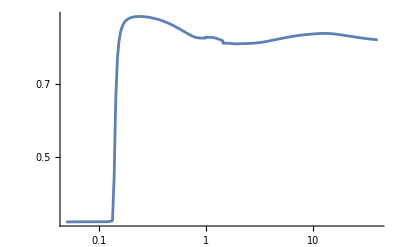

```mathematica
LLPsel=HNLsList[[1]];
Print["All processes with at least two charged/neutral particles:"]
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr,"Default"],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,40},PlotRange->All]
```

#### Mixing μ

All processes with at least two charged/neutral particles:

2ev | 2muv | 2Pimu | 2Piv | 2tauv | a1v | emuv | EtaPrv | Etav | Jets-ccv | Jets-csmu | Jets-ddv | Jets-ssv | Jets-udmu | Jets-uuv | Kmu | mutauv | Omegav | Phiv | Pi0v | Pimu
e^-
ν_e
e^+
Null | μ^-
ν_e
μ^+
Null | π^+
π^0
μ^-
Null | π^+
π^0
ν_τ
Null | τ^-
ν_e
τ^+
Null | a_1
ν_e
Null
Null | e^-
(ν̄)_e
μ^+
Null | η'
ν_e
Null
Null | η
ν_e
Null
Null | c
c̄
ν_e
Null | c
s̄
μ^-
Null | d
d̄
ν_e
Null | s
s̄
ν_e
Null | u
d̄
μ^-
Null | u
ū
ν_e
Null | K^+
μ^-
Null
Null | μ^-
(ν̄)_e
τ^+
Null | ω
ν_e
Null
Null | ϕ
ν_e
Null
Null | π^0
ν_e
Null
Null | π^+
μ^-
Null
Null

All processes with at least two charged particles:

{2ev,2muv,2Pimu,2Piv,2tauv,a1v,emuv,EtaPrv,Etav,Jets-ccv,Jets-csmu,Jets-ddv,Jets-ssv,Jets-udmu,Jets-uuv,Kmu,mutauv,Omegav,Phiv,Pimu}

Processes with jets:

{Jets-ccv,Jets-csmu,Jets-ddv,Jets-ssv,Jets-udmu,Jets-uuv}

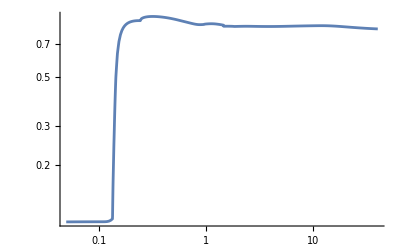

```mathematica
LLPsel=HNLsList[[2]];
Print["All processes with at least two charged/neutral particles:"]
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr,"Default"],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,40},PlotRange->All]
```

#### Mixing τ

All processes with at least two charged/neutral particles:

2ev | 2muv | 2Pitau | 2Piv | 2tauv | a1v | EtaPrv | etauv | Etav | Jets-ccv | Jets-cstau | Jets-ddv | Jets-ssv | Jets-udtau | Jets-uuv | Ktau | mutauv | Omegav | Phiv | Pi0v | Pitau
e^-
ν_e
e^+
Null | μ^-
ν_e
μ^+
Null | π^+
π^0
τ^-
Null | π^+
π^0
ν_τ
Null | τ^-
ν_e
τ^+
Null | a_1
ν_e
Null
Null | η'
ν_e
Null
Null | e^-
(ν̄)_e
τ^+
Null | η
ν_e
Null
Null | c
c̄
ν_e
Null | c
s̄
τ^-
Null | d
d̄
ν_e
Null | s
s̄
ν_e
Null | u
d̄
τ^-
Null | u
ū
ν_e
Null | K^+
τ^-
Null
Null | μ^-
(ν̄)_e
τ^+
Null | ω
ν_e
Null
Null | ϕ
ν_e
Null
Null | π^0
ν_e
Null
Null | π^+
τ^-
Null
Null

All processes with at least two charged particles:

{2ev,2muv,2Pitau,2Piv,2tauv,a1v,EtaPrv,etauv,Etav,Jets-ccv,Jets-cstau,Jets-ddv,Jets-ssv,Jets-udtau,Jets-uuv,Ktau,mutauv,Omegav,Phiv,Pitau}

Processes with jets:

{Jets-ccv,Jets-cstau,Jets-ddv,Jets-ssv,Jets-udtau,Jets-uuv}

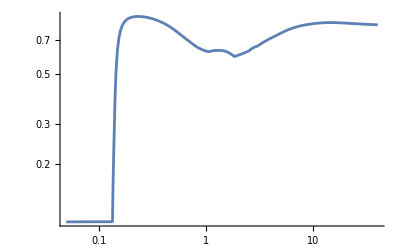

```mathematica
LLPsel=HNLsList[[3]];
Print["All processes with at least two charged/neutral particles:"]
Table[{ProcessesList[LLPsel,"True"][[i]],ListDecayProducts[LLPsel,ProcessesList[LLPsel,"True"][[i]]]},{i,1,Length[ProcessesList[LLPsel,"True"]],1}]//Transpose//TableForm
Print["All processes with at least two charged particles:"]
ProcessesList[LLPsel,"False"]
Print["Processes with jets:"]
Select[ProcessesList[LLPsel,"True"],JetsPresence[LLPsel,#]=="Yes"&]
LogLogPlot[{Evaluate[Sum[ListBrRatios[LLPsel,mN,pr,"Default"],{pr,ProcessesList[LLPsel,"True"]}]]},{mN,0.05,40},PlotRange->All]
```